Q1 c)

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x, t+Δt]]
```

```mathematica
Symbolize[Subscript[ẋ, t+Δt]]
```

```mathematica
Symbolize[Subscript[x^(..), t+Δt]]
```

```mathematica
Symbolize[Subscript[x, t+γΔt]]
```

```mathematica
Symbolize[Subscript[ẋ, t+γΔt]]
```

```mathematica
Symbolize[Subscript[x^(..), t+γΔt]]
```

```mathematica
Symbolize[Subscript[x, t]]
```

```mathematica
Symbolize[Subscript[ẋ, t]]
```

```mathematica
Symbolize[Subscript[x^(..), t]]
```

```mathematica
Symbolize[Subscript[r, t+Δt]]
```

```mathematica
Symbolize[Subscript[r, t+γΔt]]
```

```mathematica
Symbolize[Subscript[Ω, o]]
```

```mathematica
Symbolize[Subscript[Ω̄, d]]
```

```mathematica
Symbolize[ξ̄]
```

```mathematica
Symbolize[Subscript[β, 1]]
```

```mathematica
Symbolize[Subscript[β, 2]]
```

```mathematica
Symbolize[Subscript[X, t]]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
α=(-δ(6δ γ^2-12δ γ-3γ+4))/(6γ(2δ γ-1));
```

```mathematica
β=δ(Ω^2 α γ^2+1)^2;
```

```mathematica
Subscript[A, 1]=1/β(((1/4)δ^3+(-α γ+(1/8))δ^2+α(α γ^2-(γ/2)-(1/4))δ+(α/8))γ^2 Ω^4+(1/8)(16α γ^2-4)δ Ω^2+δ);
```

```mathematica
Subscript[A, 2]=1/β((2 δ^3 γ^2+(-8α γ^3+3 γ^2-4γ)δ^2+(4 α^2 γ^4-4α γ^3+10α γ^2-γ+1)δ+γ α(γ-2))Ω^4+2 Ω^2 α γ^2 δ+δ);
```

```mathematica
δ=0.3;
```

```mathematica
γ=2.78;
```

```mathematica
Ω=2 Pi p;
```

```mathematica
λ1=Subscript[A, 1]+(Subscript[A, 1]^2-Subscript[A, 2])^(1/2);
```

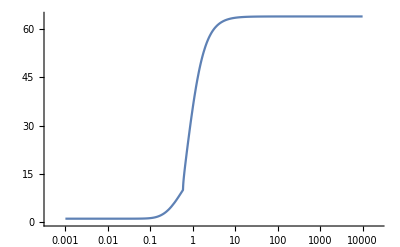

```mathematica
spR=LogLinearPlot[Abs[ λ1],{p,10^-3,10^4}]
```

```mathematica
pe=Ω/qq-1
```

-1+(2 p π)/ArcTan[(0.3 (1+3.58889 p^2)^2 √(-(11.1111 (0.3-3.76843 p^2+133.228 p^4)^2)/((1+3.58889 p^2)^4)+(3.33333 (0.3+2.15333 p^2+1234.55 p^4))/((1+3.58889 p^2)^2)))/(0.3-3.76843 p^2+133.228 p^4)]

```mathematica
-1+(2 p π)/qq
```

-1+(2 p π)/ArcTan[(0.3 (1+3.58889 p^2)^2 √((11.1111 (0.3-3.76843 p^2+133.228 p^4)^2)/((1+3.58889 p^2)^4)-(3.33333 (0.3+2.15333 p^2+1234.55 p^4))/((1+3.58889 p^2)^2)))/(0.3-3.76843 p^2+133.228 p^4)]

```mathematica
qq=ArcTan[((-Subscript[A, 1]^2+Subscript[A, 2])^(1/2))/Subscript[A, 1]]
```

ArcTan[(0.3 (1+3.58889 p^2)^2 √(-(11.1111 (0.3-3.76843 p^2+133.228 p^4)^2)/((1+3.58889 p^2)^4)+(3.33333 (0.3+2.15333 p^2+1234.55 p^4))/((1+3.58889 p^2)^2)))/(0.3-3.76843 p^2+133.228 p^4)]

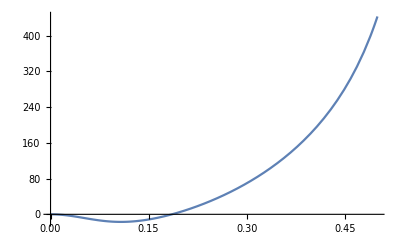

```mathematica
Plot[(pe)*100,{p,0,.5}]
```

```mathematica
ee=-1/Ω Log[Abs[λ1]]
```

-Log[Abs[(3.33333 (0.3-3.76843 p^2+133.228 p^4))/((1+3.58889 p^2)^2)+√((11.1111 (0.3-3.76843 p^2+133.228 p^4)^2)/((1+3.58889 p^2)^4)-(3.33333 (0.3+2.15333 p^2+1234.55 p^4))/((1+3.58889 p^2)^2))]]/(2 p π)

```mathematica
AD=1-Exp[-2 Pi ee Ω/qq]
```

1-Abs[(3.33333 (0.3-3.76843 p^2+133.228 p^4))/((1+3.58889 p^2)^2)+√((11.1111 (0.3-3.76843 p^2+133.228 p^4)^2)/((1+3.58889 p^2)^4)-(3.33333 (0.3+2.15333 p^2+1234.55 p^4))/((1+3.58889 p^2)^2))]^((2 π)/ArcTan[(0.3 (1+3.58889 p^2)^2 √(-(11.1111 (0.3-3.76843 p^2+133.228 p^4)^2)/((1+3.58889 p^2)^4)+(3.33333 (0.3+2.15333 p^2+1234.55 p^4))/((1+3.58889 p^2)^2)))/(0.3-3.76843 p^2+133.228 p^4)])

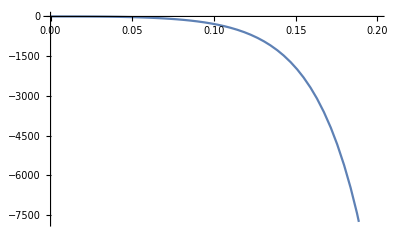

```mathematica
Plot[(AD)*100,{p,0,.2}]
```